# Achieving a Performance Target

## Supplemental material for Sec. 9.

```mathematica
?InverseCDF
```

```mathematica
T=1;r=0.02;
```

```mathematica
y[W_,t_]:=InverseCDF[NormalDistribution[0,1],ⅇ^(r(T-t))W]
```

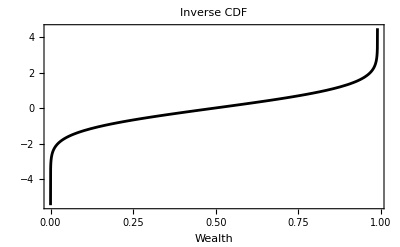

```mathematica
browneInverseCDFPlot=Plot[y[W,#1],{W,0,1},
PlotRange->{All,All},
PlotLabel->Style["Inverse CDF",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black
]&[0.5,r]
```

```mathematica
σ=1;
```

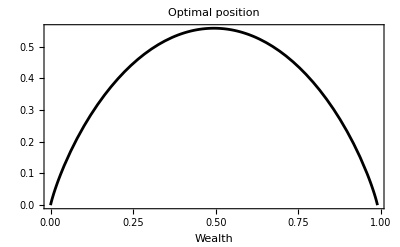

```mathematica
browneOptimalPositionPlot=Plot[1/Sqrt[2π σ^2(T-#)] Exp[-1/2 y[W,#]^2-r(T-#)],{W,0,1},
PlotRange->{All,All},
PlotLabel->Style[
"Optimal position",
FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black
]&@0.5
```

```mathematica
a=0.10;
```

```mathematica
Manipulate[
browneVelocityFunctionPlot=Plot[
{r W+((a-r)/2)/Sqrt[2π σ^2(T-#)] Exp[-1/2 y[W,#]^2-r(T-#)],
r W+(a-r)^2/(2 σ^2 η)Exp[-r(T-#)]},{W,0,1},
PlotRange->{All,All},
PlotLabel->Style["Velocity function",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black]&@0.5,
{η,0.01,1}]
```

```mathematica
Wmax=NMaximize[((a-r)/2)/Sqrt[2π σ^2(T-#)] Exp[-1/2 y[W,#]^2-r(T-#)]&@0.5,W]
```

{0.022343,{W→0.495025}}

```mathematica
W/.Wmax[[2]]
```

0.495025

```mathematica
ηSol=Flatten@NSolve[((a-r)/2)/Sqrt[2π σ^2(T-#)] Exp[-1/2 y[W/.Wmax[[2]],#]^2]&@0.5==(a-r)^2/(2 σ^2 η),η]
```

{η→0.141796}

```mathematica
position=(a-r)/(σ^2 η)Exp[-r(T-0.5)]/.ηSol
```

0.558576

```mathematica
fractionalPosition=position/(W/.Wmax[[2]])
```

1.12838

```mathematica
Flatten@NSolve[((a-r)/(σ^2 η))Exp[-r(T-0.5)]==(W/.Wmax[[2]]),η]
```

{η→0.16}

### Export

```mathematica
writeDirectory=NotebookDirectory[]<>"/output/browne";
```

```mathematica
SetDirectory@writeDirectory
```

```mathematica
Export["browneInverseCDFPlot.pdf",browneInverseCDFPlot]
```

browneInverseCDFPlot.pdf

```mathematica
Export["browneOptimalPositionPlot.pdf",browneOptimalPositionPlot]
```

browneOptimalPositionPlot.pdf

```mathematica
Export["browneVelocityFunctionPlot.pdf",browneVelocityFunctionPlot]
```

browneVelocityFunctionPlot.pdf